# Recursive Geometry

## Toward the Koch snowflake

### Start with an equilateral triangle.

An equilateral triangle has three angles of 60 degrees. We can use this 60-degree fact to render an equilateral triangle in Polar Coordinates:

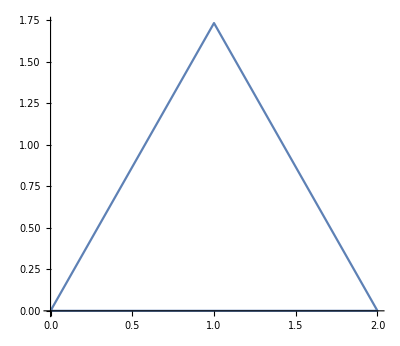

```mathematica
origin:={0,0}; equilateralAngle:=60 Degree; r:=2; 
plotPoints:={origin,{0,r},{equilateralAngle,r},origin};
ListPolarPlot[plotPoints, Joined->True]
```

### Rotate a copy around by 180 degrees.

A copy of this triangle can be generated by rotating the plot points around by 180 degrees.

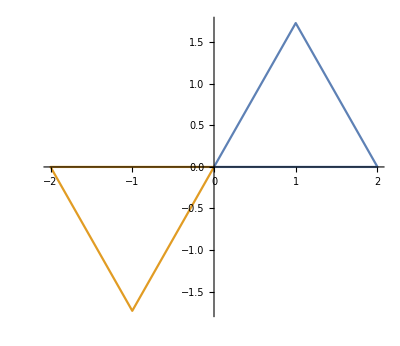

```mathematica
plotPoints2:=plotPoints+Table[{180Degree,0},{4}];
polarPlot=ListPolarPlot[{plotPoints,plotPoints2}, Joined->True]
```

### Convert the Polar plot points to Cartesian coordinates to get the centroid.

We would like to “stack” these triangles on top of each other, using the centroid of the triangles.
The centroid formula: ((x_1+x_2+x_3)/3,(y_1+y_2+y_3)/3) where (x_1, y_1), (x_2, y_2) and (x_3, y_3) are the coordinates of the triangle.
To obtain the coordinates of the triangle from our Polar coordinates, we use the conversion formulae: x = r × cos(θ) and y = r × sin(θ).

```mathematica
x[r_,θ_]:=r*Cos[θ];
y[r_,θ_]:=r*Sin[θ];
x1:=x[0,0];y1:=y[0,0];
x2:=x[r,0];y2:=y[r,0];
x3:=x[r,equilateralAngle];y3:=y[r,equilateralAngle];
centroid:={(x1+x2+x3)/3,(y1+y2+y3)/3};
N[centroid]
```

{1.,0.57735}

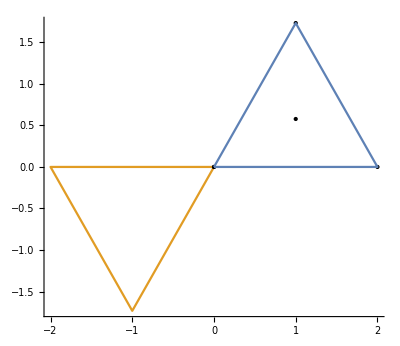

```mathematica
cartesianVector:={{x1,y1},{x2,y2},{x3,y3},{x1,y1}};
points:={PointSize[Large],Point[Append[cartesianVector, centroid]]};
Show[Graphics[points],polarPlot,Axes->True]
```

### Center the triangles using the centroid.

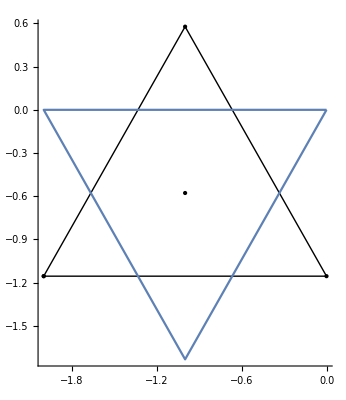

```mathematica
polarPlot:=ListPolarPlot[plotPoints2, Joined->True];
transformedCartesianVector:=cartesianVector-Table[centroid*2,{4}];
points:={PointSize[Large],Point[Append[transformedCartesianVector,centroid*-1]]};
pointsAndLines:={points, Line[transformedCartesianVector]};
Show[Graphics[pointsAndLines],polarPlot,Axes->True]
```